```mathematica
Import["http://mahtblog.files.wordpress.com/2011/03/grafmaht.png"]
```

```mathematica
puntos = {{62.,76.6666},{62.6667,98.},{64.6667,121.333},{67.3333,164.},{70.,206.},{74.,256.667},{77.3333,288.667},{80.,302.667},{83.3333,311.333},{87.3333,302.667},{95.3333,240.},{101.333,166.},{107.333,94.6666},{113.333,41.3333},{118.,24.6666},{120.667,20.6666},{124.667,25.3333},{134.667,94.6666},{142.667,159.333},{149.333,199.333},{156.667,216.667},{163.333,200.667},{172.,158.},{180.,104.667},{188.,68.},{193.333,62.},{200.667,70.},{215.333,133.333},{221.333,155.333},{228.667,166.667},{238.,154.667},{249.333,116.667},{260.,90.6666},{266.,84.},{274.,90.},{285.333,114.667},{293.333,132.},{300.667,140.},{311.333,132.667},{324.667,109.333},{334.667,96.6666},{338.667,96.},{346.667,97.3333},{362.,116.667},{374.667,124.667},{386.667,118.667},{400.,106.667},{410.,101.333},{422.,105.333},{436.667,114.667},{446.667,117.333},{459.333,114.667},{469.333,109.333},{480.667,106.},{492.667,106.},{499.333,107.333}};
```

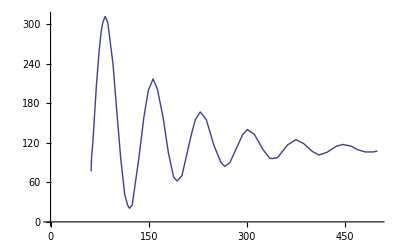

```mathematica
ListLinePlot[puntos]
```

```mathematica
.
```

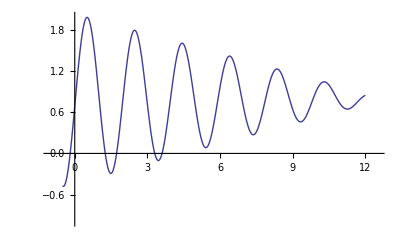

```mathematica
f[x_]:=-24*(0.103-0.008x)*0.5Cos[ 3.2x-4.8]+0.8;
Plot[f[x],{x,-0.5,12},PlotRange->{{-1,12.5},{-1,2}}]
```

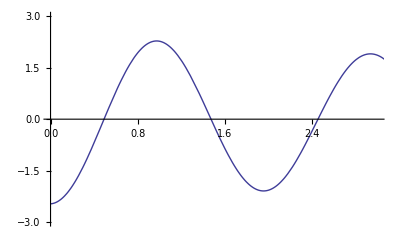

```mathematica
Plot[f[x], {x, 0, 15}, PlotRange->{{0, 3}, {-3, 3}}, Epilog->Map[Point, puntos]]
```

```mathematica
Clear[a1,a2,a3,a4,a5,a6,a7]
```

{a→205.873,b→-8268.23,c→196086.,d→-2.07649×10^6,a2→-3.37303,b2→0.0383288,c2→-0.00030949,d2→1.7802×10^-6,e→-7.11439×10^-9,f→1.814×10^-11,i→-2.05556×10^-14,j→-2.96071×10^-17,k→1.25673×10^-19,l→-2.78202×10^-23,m→-4.76982×10^-25,n→4.68498×10^-28,o→1.63443×10^-30,p→-3.21642×10^-33,q→-3.88257×10^-36,r→2.01658×10^-38,s→-2.93864×10^-41,t→2.02543×10^-44,u→-5.65144×10^-48,v→0.,w→0.,y→0.}

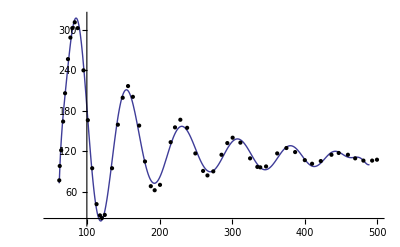

{a→194.712,b→-7889.,c→188726.,d→-2.01627×10^6,a2→-3.16094,b2→0.0355587,c2→-0.000283804,d2→1.6091×10^-6,e→-6.30342×10^-9,f→1.55263×10^-11,i→-1.56227×10^-14,j→-3.12339×10^-17,k→1.09822×10^-19,l→7.0747×10^-25,m→-4.49468×10^-25,n→3.36842×10^-28,o→1.64561×10^-30,p→-2.75705×10^-33,q→-4.38358×10^-36,r→1.94096×10^-38,s→-2.71469×10^-41,t→1.82228×10^-44,u→-4.97526×10^-48,v→0.,w→0.,y→0.}

```mathematica
modelo=  a x^3+b x^2+c x +d+a2 x^4+b2 x^5+c2 x^6+d2 x^7+e x^8+f x^9+i x^10+j x^11+k x^12+l x^13+m x^14+n x^15+o x^16+p x^17+q x^18+r x^19+s x^20+t x^21+u x^22;

regresion =FindFit[puntos,modelo,{a,b,c,d,a2,b2,c2,d2,e,f,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,y},x]
regreF = Function[{}, Evaluate[modelo/.regresion]];
Plot[regreF[x], {x, 62, 489}, PlotRange->{{50, 500}, {15, 320}}, Epilog->Map[Point, puntos]]
```

```mathematica
Clear[a]
```

```mathematica
g[x_]:=Exp[a x*Cos[b x+c]+d]
```

```mathematica
Plot[g[x],{x,0, 15}]
```

-Graphics-

```mathematica
Clear[a,b,c,d,e]
```

e+ⅇ^(d+Cos[c+b x])

{a→1.,b→1.03021,c→-10.1163,d→2.44282,e→118.682}

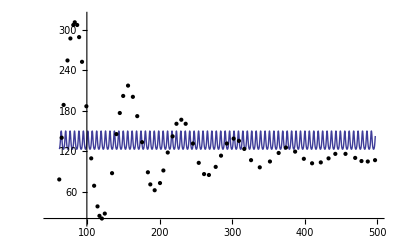

```mathematica
modelo= Exp[Cos[b x+c]+d]+e
regresion =FindFit[puntos,modelo,{a,b,c,d,e},x]
regreF = Function[{}, Evaluate[modelo/.regresion]];
Plot[regreF[x], {x, 62, 497}, PlotRange->{{50, 500}, {15, 320}}, Epilog->Map[Point, puntos]]
```

```mathematica
funcion[y_]:=regreF[[2]]/.x->y
```

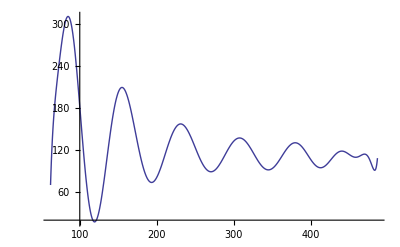

```mathematica
Plot[funcion[y],{y,62,487}]
```

```mathematica
regreF
```

Function[{},-2.02937×10^6+189981. x-7943.04 x^2+196.096 x^3-3.18448 x^4+0.0358386 x^5-0.00028619 x^6+1.62371×10^-6 x^7-6.36631×10^-9 x^8+1.57022×10^-11 x^9-1.58588×10^-14 x^10-3.14779×10^-17 x^11+1.1125×10^-19 x^12-1.14236×10^-26 x^13-4.55083×10^-25 x^14+3.44506×10^-28 x^15+1.66562×10^-30 x^16-2.80815×10^-33 x^17-4.42872×10^-36 x^18+1.97298×10^-38 x^19-2.76692×10^-41 x^20+1.86171×10^-44 x^21-5.09487×10^-48 x^22]

```mathematica
ret[x_]:=(-2.0293723434851132*^6+189981.22521317823 x-7943.035714181121 x^2+196.09626804596758 x^3-3.18447801947162 x^4+0.03583860158373511 x^5-0.0002861895487217661 x^6+1.6237123263053717*^-6 x^7-6.3663070662586295*^-9 x^8+1.5702178880101494*^-11 x^9-1.5858839137880024*^-14 x^10-3.1477862300095126*^-17 x^11+1.1124961505813676*^-19 x^12-1.142356203263974*^-26 x^13-4.55082865924211*^-25 x^14+3.4450582843452545*^-28 x^15+1.665623492642352*^-30 x^16-2.8081502740834326*^-33 x^17-4.428722238209209*^-36 x^18+1.9729835337588506*^-38 x^19-2.7669177783416694*^-41 x^20+1.8617129766138767*^-44 x^21-5.094871246873843*^-48 x^22)
```

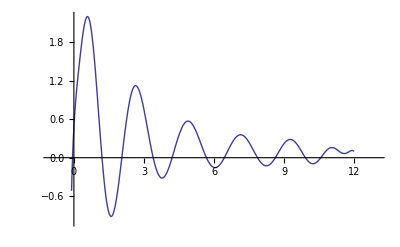

```mathematica
Plot[0.0106ret[34 y+65]-1.1,{y,-0.1,12}, PlotRange->{{-1,13},{-1,2.2}}]
```